```mathematica
MulPolBinom[x_,y_]:=
Module[{a,d,i,j},
d=Length[x];
i=d+1;
a=Table[0,{i}];
a[[1]]=x[[1]]*y;
a[[i]]=x[[d]];
For[j=2,j≤d,j++,a[[j]]=x[[j]]*y+x[[j-1]]];
a]
```

```mathematica
MulPolBinom[{5,4,-1,3},2]
```

{10,13,2,5,3}

```mathematica
Lk[points_,k_]:=
Module[{coefs,j,c},
coefs={1};
 c=Length[points];
For[j=1,j≤c,j++,  
If[j≠k,coefs=MulPolBinom[coefs,-points[[j]]]/(points[[k]]-points[[j]])]];
coefs]
```

```mathematica
pcoef=Lk[{-1,2,4},3]
```

{-1/5,-1/10,1/10}

```mathematica
EvalPol[x_,b_]:=
Module[{c,d,j},
d=Length[x];
c=0;
For[j=d,2≤j,j--,c=c+b^(j-1)*x[[j]]];
c=c+x[[1]];
c]
```

```mathematica
PolValues[p_,b_]:=
Module[{c,i},
c=Table[EvalPol[p,b[[i]]],{i,Length[b]}];
c]
```

```mathematica
PolValues[pcoef,{-1,2,4}]
```

```mathematica
{0,0,1}
```

{0,0,1}

```mathematica
LagrangePol[points_,values_]:=
Module[{i,a,p},
p=0;
a=Length[values];
For[i=1,i≤a,i++,
p=p+values[[i]]*Lk[points,i]];
p]
```

```mathematica
points={2,3,-1,5}; values={3,11,-9,69};
```

```mathematica
fcoefs=LagrangePol[points,values]
```

{-1,4,-3,1}

```mathematica
EvalPol[fcoefs,5]
```

69

```mathematica
PolValues[fcoefs,points]
```

{3,11,-9,69}

```mathematica
FindSegment[xs_,x_]:=
Module[{k,n},
n=Length[xs];
If[(xs[[1]]≤x),
k=1;
While[(x≥xs[[k+1]])&&(k<n-1),k++];
];
k]
```

```mathematica
FindSegment[{10,20},10]
```

1

```mathematica
FindSegment[{10,12,15,19,20,29,30},12]
```

2

```mathematica
FindSegment[{10,12,15,19,20,29,30},29]
```

6

```mathematica
FindSegment[{10,12,15,19,20,29,30},30]
```

6

```mathematica
LinSpline[xs_,as_,bs_,x_]:=
Module[{S,j,i,n},
n=FindSegment[xs,x];
j=x-xs[[n]];
S=as[[n]]+bs[[n]]*j;
S]
```

```mathematica
LinSpline[{1,5,7,8},{3,-1,0},{-1,1/2,3},1]
```

3

```mathematica
xs={1,5,7,8}; as={3,-1,0};bs={-1,1/2,3};
```

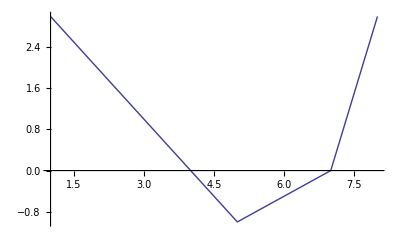

```mathematica
Plot[LinSpline[xs,as,bs,x],{x,1,8}]
```

```mathematica
p1=Plot[(-Sin[x]+100*x)*0.01Cos[x],{x,5,20},PlotLabel->f[x]==(-Sin[x]+100*x)*0.01Cos[x],PlotStyle->Orange];
```

```mathematica
f[x1_]:=(-Sin[x1]+100*x1)*0.01Cos[x1];
points={5,9,9.5,11,12.5,13.7,14.8,15.2,16.2,17.6,18.7,19.3,20}; 
values=Map[f,points];
fcoefs1=LagrangePol[points,values]
```

{53010.3,-66716.1,37202.9,-12179.9,2610.76,-386.213,40.4432,-3.02186,0.160006,-0.00586128,0.000141185,-2.01099×10^-6,1.28305×10^-8}

```mathematica
f1[x_]:=53010.34274032444-66716.1103301536x+37202.858338242106x^2-12179.908340046371x^3+2610.758153193943x^4-386.2127291888987x^5+40.4431502312039x^6-3.0218602363269866x^7+0.16000606773643178x^8-0.005861281644868429x^9+0.00014118517657972648x^10-2.010990168064929*10^-6x^11+1.2830519132140011*10^-8x^12
```

```mathematica
p2=Plot[f1[x],{x,5,20},PlotStyle->Green];
```

```mathematica
p3=ListPlot[Transpose[{points,values}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[p1,p2,p3]
```

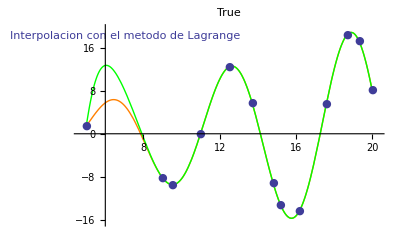

```mathematica
points0={0,6,19,26,31,35,36};
values0={13,8,-2,-4.2,-3.3,-1,0};
fcoefsv0=LagrangePol[points0,values0]
```

{13.,-1.61728,0.253706,-0.0275358,0.00133998,-0.0000296032,2.48285×10^-7}

```mathematica
j0[x_]:=13.-1.6172835962350058x+0.2537061449657214x^2-0.027535781727449332x^3+0.001339984508252054x^4-0.000029603229371771747x^5+2.482853367909691*10^-7x^6
s0=Plot[j0[x],{x,0,36},PlotRange->{-10,22},PlotStyle->Red];
d0=ListPlot[Transpose[{points0,values0}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
points1={0,6,13,19,21,25,27.2,33.2,36};
values1={0,8,13,15,15,14,13,7,0};
fcoefsv1=LagrangePol[points1,values1]
```

{0.,0.79779,0.371328,-0.0828175,0.00818486,-0.000442255,0.00001333,-2.09926×10^-7,1.34064×10^-9}

```mathematica
j1[x_]:=0+0.797789665966766x+0.3713284307949305x^2-0.08281750226706952x^3+0.008184862169159271x^4-0.00044225495983568446x^5+0.000013330038544136398x^6-2.09926058591471*10^-7x^7+1.340642470216795*10^-9x^8
s1=Plot[j1[x],{x,0,36},PlotStyle->Red];
d1=ListPlot[Transpose[{points1,values1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
points2={19,20,21.5,24,25};
values2={15,17,20,16,14};
fcoefsv2=LagrangePol[points2,values2]
```

{12465.4,-2319.64,160.947,-4.9281,0.0561905}

```mathematica
j2[x_]:=12465.428571428576-2319.640476190477x+160.94666666666672x^2-4.9280952380952385x^3+0.05619047619047626x^4
s2=Plot[j2[x],{x,19,25},PlotStyle->Orange];
d2=ListPlot[Transpose[{points2,values2}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
points3={21,22.2,24.9,25.9,27};
values3={5,7.2,9.9,7,5};
fcoefsv3=LagrangePol[points3,values3]
```

{26833.6,-4535.09,286.07,-7.98014,0.0830706}

```mathematica
j3[x_]:=26833.55663086913-4535.092277735135x+286.0699280074278x^2-7.980144051572624x^3+0.08307061878490454x^4
s3=Plot[j3[x],{x,21,27},PlotStyle->Brown];
d3=ListPlot[Transpose[{points3,values3}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
points4={31,31.3,32.1,35};
values4={-3.3,-1.4,-0.3,-1};
fcoefsv4=LagrangePol[points4,values4]
```

{-36270.6,3309.79,-100.576,1.01768}

```mathematica
j4[x_]:=-36270.609135389146+3309.7945910644025x-100.5764847920016x^2+1.0176791211273923x^3
s4=Plot[j4[x],{x,31,35},PlotStyle->Black];
d4=ListPlot[Transpose[{points4,values4}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
points5={0,1,1.2};
values5={0,4.5,6};
fcoefsv5=LagrangePol[points5,values5]
```

{0.,2.,2.5}

```mathematica
j5[x_]:=0+1.9999999999999964x+2.5000000000000036x^2
s5=Plot[j5[x],{x,0,1.2},PlotStyle->Red];
d5=ListPlot[Transpose[{points5,values5}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
points6={1.2,0.2,0};
values6={6,9,13};
fcoefsv6=LagrangePol[points6,values6]
```

{13.,-22.8333,14.1667}

```mathematica
j6[x_]:=13-22.833333333333343x+14.166666666666671x^2
s6=Plot[j6[x],{x,0,1.2},PlotStyle->Red];
d6=ListPlot[Transpose[{points6,values6}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[s0,s1,s2,s3,s4,s5,s6,d0,d1,d2,d3,d4,d5,d6]
```

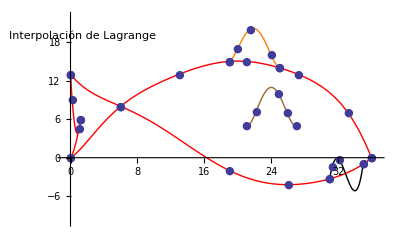

```mathematica
xsv0={8.5,9,10,10.6};
ysv0={3.5,5.3,5.2,4};
fcoefsr0=LagrangePol[xsv0,ysv0]
```

{-681.782,199.962,-19.2177,0.609127}

```mathematica
z0[x_]:=-681.7821428571438+199.96210317460344x-19.217658730158675x^2+0.6091269841269842x^3
w0=Plot[z0[x],{x,8.5,10.6},PlotStyle->Red];
k0=ListPlot[Transpose[{xsv0,ysv0}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv1={8.5,9,10.1,12.3,13.6};
ysv1={3.5,2,1.1,2,4.2};
fcoefsr1=LagrangePol[xsv1,ysv1]
```

{819.162,-291.027,38.7655,-2.29383,0.0509486}

```mathematica
z1[x_]:=819.1617267691751-291.02669937412156x+38.76554068756616x^2-2.293832771812187x^3+0.05094861493006351x^4
w1=Plot[z1[x],{x,8.5,13.6},PlotStyle->Red];
k1=ListPlot[Transpose[{xsv1,ysv1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv2={13,13.6};
ysv2={12,4.2};
fcoefsr2=LagrangePol[xsv2,ysv2]
```

{181.,-13.}

```mathematica
z2[x_]:=181.00000000000006-13.000000000000007x
w2=Plot[z2[x],{x,13,13.6},PlotStyle->Red];
k2=ListPlot[Transpose[{xsv2,ysv2}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv3={13,13.1,13.2};
ysv3={12,14.5,17};
fcoefsr3=LagrangePol[xsv3,ysv3]
```

{-313.,25.,1.13687×10^-13}

```mathematica
z3[x_]:=-313+24.999999999996362x+1.1368683772161603*10^-13x^2
w3=Plot[z3[x],{x,13,13.2},PlotStyle->Red];
k3=ListPlot[Transpose[{xsv3,ysv3}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv4={9.4,10,12,13.2};
ysv4={12.3,14,16,17};
fcoefsr4=LagrangePol[xsv4,ysv4]
```

{-274.467,72.6747,-6.10134,0.171854}

```mathematica
z4[x_]:=-274.46659919028275+72.67467948717922x-6.101341093117405x^2+0.17185391363022862x^3
w4=Plot[z4[x],{x,9.4,13.2},PlotStyle->Red];
k4=ListPlot[Transpose[{xsv4,ysv4}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv5={9.4,10,12,14.5,15.4};
ysv5={12.3,10,9,10,12};
fcoefsr5=LagrangePol[xsv5,ysv5]
```

{1156.13,-366.32,43.7095,-2.31117,0.0457299}

```mathematica
z5[x_]:=1156.1288382399514-366.32036447374185x+43.70945477906261x^2-2.3111697670521254x^3+0.045729909564332316x^4
w5=Plot[z5[x],{x,9.4,15.4},PlotStyle->Red];
k5=ListPlot[Transpose[{xsv5,ysv5}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[w0,w1,w2,w3,w4,w5,k0,k1,k2,k3,k4,k5,PlotRange->All]
```